### Start choosing the example:

```mathematica
t=27;
beta = 0;
A = 0.2;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4,5,6,7,8,9,10},Adjacency Matrix→{{0,1,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,80}},Exit Vertices and Terminal Costs→{{10,15}},Switching Costs→{}|>

```mathematica
Data["Entrance Vertices and Currents"]={{1,1}};
Data["Exit Vertices and Terminal Costs"]={{10,1000}};
```

```mathematica
MFGEquations=DataToEquations[Data];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.013493,Null}

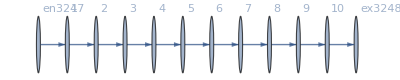

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j3249→1.,j3250→1.,j3251→1.,j3252→1.,j3253→1.,j3254→1.,j3255→1.,j3256→1.,j3257→1.,j3258→1.,j3259→1.,j3260→0.,j3261→0.,j3262→0.,j3263→0.,j3264→0.,j3265→0.,j3266→0.,j3267→0.,j3268→0.,j3269→0.,j3270→0.,jt3271→0.,jt3272→1.,jt3273→1.,jt3274→0.,jt3275→1.,jt3276→0.,jt3277→1.,jt3278→0.,jt3279→1.,jt3280→0.,jt3281→1.,jt3282→0.,jt3283→1.,jt3284→0.,jt3285→1.,jt3286→0.,jt3287→1.,jt3288→0.,jt3289→1.,jt3290→0.,u3291→1009.,u3292→1008.,u3293→1007.,u3294→1006.,u3295→1005.,u3296→1004.,u3297→1003.,u3298→1002.,u3299→1001.,u3300→1000.,u3301→1009.,u3302→-1.+1. 1009.,u3303→-1.+1. 1008.,u3304→-1.+1. 1007.,u3305→-1.+1. 1006.,u3306→-1.+1. 1005.,u3307→-1.+1. 1004.,u3308→-1.+1. 1003.,u3309→-1.+1. 1002.,u3310→-1.+1. 1001.,u3311→1000.,u3312→0.+1. 1009.|>

```mathematica
Data
```

<|Vertices List→{1,2,3,4,5,6,7,8,9,10},Adjacency Matrix→{{0,1,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,1}},Exit Vertices and Terminal Costs→{{10,1000}},Switching Costs→{}|>

#### Non-linear case

```mathematica
alpha = 0;
FFR= FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The relative Error on the nonlinear terms is 1.56361×10^-12

FRX1: The relative Error on the nonlinear terms is 1.56361×10^-12

<|j3249→1,j3250→1,j3251→1,j3252→1,j3253→1,j3254→1,j3255→1,j3256→1,j3257→1,j3258→1,j3259→1,j3260→0.,j3261→0.,j3262→0.,j3263→0.,j3264→0.,j3265→0.,j3266→0.,j3267→0.,j3268→0.,j3269→0.,j3270→0.,jt3271→0.,jt3272→1,jt3273→1,jt3274→0.,jt3275→1,jt3276→0.,jt3277→1,jt3278→0.,jt3279→1,jt3280→0.,jt3281→1,jt3282→0.,jt3283→1,jt3284→0.,jt3285→1,jt3286→0.,jt3287→1,jt3288→0.,jt3289→1,jt3290→0.,u3291→1012.07,u3292→1010.72,u3293→1009.38,u3294→1008.04,u3295→1006.7,u3296→1005.36,u3297→1004.02,u3298→1002.68,u3299→1001.34,u3300→1000.,u3301→0.+1. 1012.07,u3302→1010.72,u3303→1009.38,u3304→1008.04,u3305→1006.7,u3306→1005.36,u3307→1004.02,u3308→1002.68,u3309→1001.34,u3310→1000.,u3311→1000.,u3312→0.+1. (0.+1. 1012.07)|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The relative Error on the nonlinear terms is 5.13478×10^-13

FRX1: The relative Error on the nonlinear terms is 5.13478×10^-13

<|j3249→1,j3250→1,j3251→1,j3252→1,j3253→1,j3254→1,j3255→1,j3256→1,j3257→1,j3258→1,j3259→1,j3260→0.,j3261→0.,j3262→0.,j3263→0.,j3264→0.,j3265→0.,j3266→0.,j3267→0.,j3268→0.,j3269→0.,j3270→0.,jt3271→0.,jt3272→1,jt3273→1,jt3274→0.,jt3275→1,jt3276→0.,jt3277→1,jt3278→0.,jt3279→1,jt3280→0.,jt3281→1,jt3282→0.,jt3283→1,jt3284→0.,jt3285→1,jt3286→0.,jt3287→1,jt3288→0.,jt3289→1,jt3290→0.,u3291→1011.88,u3292→1010.56,u3293→1009.24,u3294→1007.92,u3295→1006.6,u3296→1005.28,u3297→1003.96,u3298→1002.64,u3299→1001.32,u3300→1000.,u3301→0.+1. 1011.88,u3302→1010.56,u3303→1009.24,u3304→1007.92,u3305→1006.6,u3306→1005.28,u3307→1003.96,u3308→1002.64,u3309→1001.32,u3310→1000.,u3311→1000.,u3312→0.+1. (0.+1. 1011.88)|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The relative Error on the nonlinear terms is 6.10187×10^-13

FRX1: The relative Error on the nonlinear terms is 6.10187×10^-13

<|j3249→1,j3250→1,j3251→1,j3252→1,j3253→1,j3254→1,j3255→1,j3256→1,j3257→1,j3258→1,j3259→1,j3260→0.,j3261→0.,j3262→0.,j3263→0.,j3264→0.,j3265→0.,j3266→0.,j3267→0.,j3268→0.,j3269→0.,j3270→0.,jt3271→0.,jt3272→1,jt3273→1,jt3274→0.,jt3275→1,jt3276→0.,jt3277→1,jt3278→0.,jt3279→1,jt3280→0.,jt3281→1,jt3282→0.,jt3283→1,jt3284→0.,jt3285→1,jt3286→0.,jt3287→1,jt3288→0.,jt3289→1,jt3290→0.,u3291→1011.46,u3292→1010.18,u3293→1008.91,u3294→1007.64,u3295→1006.36,u3296→1005.09,u3297→1003.82,u3298→1002.55,u3299→1001.27,u3300→1000.,u3301→0.+1. 1011.46,u3302→1010.18,u3303→1008.91,u3304→1007.64,u3305→1006.36,u3306→1005.09,u3307→1003.82,u3308→1002.55,u3309→1001.27,u3310→1000.,u3311→1000.,u3312→0.+1. (0.+1. 1011.46)|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The relative Error on the nonlinear terms is 7.59637×10^-12

FRX1: The relative Error on the nonlinear terms is 7.59637×10^-12

<|j3249→1,j3250→1,j3251→1,j3252→1,j3253→1,j3254→1,j3255→1,j3256→1,j3257→1,j3258→1,j3259→1,j3260→0.,j3261→0.,j3262→0.,j3263→0.,j3264→0.,j3265→0.,j3266→0.,j3267→0.,j3268→0.,j3269→0.,j3270→0.,jt3271→0.,jt3272→1,jt3273→1,jt3274→0.,jt3275→1,jt3276→0.,jt3277→1,jt3278→0.,jt3279→1,jt3280→0.,jt3281→1,jt3282→0.,jt3283→1,jt3284→0.,jt3285→1,jt3286→0.,jt3287→1,jt3288→0.,jt3289→1,jt3290→0.,u3291→1009.49,u3292→1008.44,u3293→1007.38,u3294→1006.33,u3295→1005.27,u3296→1004.22,u3297→1003.16,u3298→1002.11,u3299→1001.05,u3300→1000.,u3301→0.+1. 1009.49,u3302→1008.44,u3303→1007.38,u3304→1006.33,u3305→1005.27,u3306→1004.22,u3307→1003.16,u3308→1002.11,u3309→1001.05,u3310→1000.,u3311→1000.,u3312→0.+1. (0.+1. 1009.49)|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

FRX1: The relative Error on the nonlinear terms is ∞

<|j3249→1,j3250→1,j3251→1,j3252→1,j3253→1,j3254→1,j3255→1,j3256→1,j3257→1,j3258→1,j3259→1,j3260→0.,j3261→0.,j3262→0.,j3263→0.,j3264→0.,j3265→0.,j3266→0.,j3267→0.,j3268→0.,j3269→0.,j3270→0.,jt3271→0.,jt3272→1,jt3273→1,jt3274→0.,jt3275→1,jt3276→0.,jt3277→1,jt3278→0.,jt3279→1,jt3280→0.,jt3281→1,jt3282→0.,jt3283→1,jt3284→0.,jt3285→1,jt3286→0.,jt3287→1,jt3288→0.,jt3289→1,jt3290→0.,u3291→1009.,u3292→1008.,u3293→1007.,u3294→1006.,u3295→1005.,u3296→1004.,u3297→1003.,u3298→1002.,u3299→1001.,u3300→1000.,u3301→0.+1. 1009.,u3302→1008.,u3303→1007.,u3304→1006.,u3305→1005.,u3306→1004.,u3307→1003.,u3308→1002.,u3309→1001.,u3310→1000.,u3311→1000.,u3312→0.+1. (0.+1. 1009.)|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The relative Error on the nonlinear terms is 2.11517×10^-12

FRX1: The relative Error on the nonlinear terms is 2.11517×10^-12

<|j3249→1,j3250→1,j3251→1,j3252→1,j3253→1,j3254→1,j3255→1,j3256→1,j3257→1,j3258→1,j3259→1,j3260→0.,j3261→0.,j3262→0.,j3263→0.,j3264→0.,j3265→0.,j3266→0.,j3267→0.,j3268→0.,j3269→0.,j3270→0.,jt3271→0.,jt3272→1,jt3273→1,jt3274→0.,jt3275→1,jt3276→0.,jt3277→1,jt3278→0.,jt3279→1,jt3280→0.,jt3281→1,jt3282→0.,jt3283→1,jt3284→0.,jt3285→1,jt3286→0.,jt3287→1,jt3288→0.,jt3289→1,jt3290→0.,u3291→1007.78,u3292→1006.91,u3293→1006.05,u3294→1005.19,u3295→1004.32,u3296→1003.46,u3297→1002.59,u3298→1001.73,u3299→1000.86,u3300→1000.,u3301→0.+1. 1007.78,u3302→1006.91,u3303→1006.05,u3304→1005.19,u3305→1004.32,u3306→1003.46,u3307→1002.59,u3308→1001.73,u3309→1000.86,u3310→1000.,u3311→1000.,u3312→0.+1. (0.+1. 1007.78)|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The relative Error on the nonlinear terms is 9.4181×10^-13

FRX1: The relative Error on the nonlinear terms is 9.4181×10^-13

<|j3249→1,j3250→1,j3251→1,j3252→1,j3253→1,j3254→1,j3255→1,j3256→1,j3257→1,j3258→1,j3259→1,j3260→0.,j3261→0.,j3262→0.,j3263→0.,j3264→0.,j3265→0.,j3266→0.,j3267→0.,j3268→0.,j3269→0.,j3270→0.,jt3271→0.,jt3272→1,jt3273→1,jt3274→0.,jt3275→1,jt3276→0.,jt3277→1,jt3278→0.,jt3279→1,jt3280→0.,jt3281→1,jt3282→0.,jt3283→1,jt3284→0.,jt3285→1,jt3286→0.,jt3287→1,jt3288→0.,jt3289→1,jt3290→0.,u3291→1005.03,u3292→1004.47,u3293→1003.91,u3294→1003.35,u3295→1002.8,u3296→1002.24,u3297→1001.68,u3298→1001.12,u3299→1000.56,u3300→1000.,u3301→0.+1. 1005.03,u3302→1004.47,u3303→1003.91,u3304→1003.35,u3305→1002.8,u3306→1002.24,u3307→1001.68,u3308→1001.12,u3309→1000.56,u3310→1000.,u3311→1000.,u3312→0.+1. (0.+1. 1005.03)|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The relative Error on the nonlinear terms is 5.12035×10^-13

FRX1: The relative Error on the nonlinear terms is 5.12035×10^-13

<|j3249→1,j3250→1,j3251→1,j3252→1,j3253→1,j3254→1,j3255→1,j3256→1,j3257→1,j3258→1,j3259→1,j3260→0.,j3261→0.,j3262→0.,j3263→0.,j3264→0.,j3265→0.,j3266→0.,j3267→0.,j3268→0.,j3269→0.,j3270→0.,jt3271→0.,jt3272→1,jt3273→1,jt3274→0.,jt3275→1,jt3276→0.,jt3277→1,jt3278→0.,jt3279→1,jt3280→0.,jt3281→1,jt3282→0.,jt3283→1,jt3284→0.,jt3285→1,jt3286→0.,jt3287→1,jt3288→0.,jt3289→1,jt3290→0.,u3291→1003.77,u3292→1003.35,u3293→1002.93,u3294→1002.51,u3295→1002.09,u3296→1001.68,u3297→1001.26,u3298→1000.84,u3299→1000.42,u3300→1000.,u3301→0.+1. 1003.77,u3302→1003.35,u3303→1002.93,u3304→1002.51,u3305→1002.09,u3306→1001.68,u3307→1001.26,u3308→1000.84,u3309→1000.42,u3310→1000.,u3311→1000.,u3312→0.+1. (0.+1. 1003.77)|>

```mathematica
alpha = 1.6001;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],200,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The relative Error on the nonlinear terms is 5.02015×10^-13

FRX1: The relative Error on the nonlinear terms is 5.02015×10^-13

<|j3249→1,j3250→1,j3251→1,j3252→1,j3253→1,j3254→1,j3255→1,j3256→1,j3257→1,j3258→1,j3259→1,j3260→0.,j3261→0.,j3262→0.,j3263→0.,j3264→0.,j3265→0.,j3266→0.,j3267→0.,j3268→0.,j3269→0.,j3270→0.,jt3271→0.,jt3272→1,jt3273→1,jt3274→0.,jt3275→1,jt3276→0.,jt3277→1,jt3278→0.,jt3279→1,jt3280→0.,jt3281→1,jt3282→0.,jt3283→1,jt3284→0.,jt3285→1,jt3286→0.,jt3287→1,jt3288→0.,jt3289→1,jt3290→0.,u3291→1003.77,u3292→1003.35,u3293→1002.93,u3294→1002.51,u3295→1002.09,u3296→1001.68,u3297→1001.26,u3298→1000.84,u3299→1000.42,u3300→1000.,u3301→0.+1. 1003.77,u3302→1003.35,u3303→1002.93,u3304→1002.51,u3305→1002.09,u3306→1001.68,u3307→1001.26,u3308→1000.84,u3309→1000.42,u3310→1000.,u3311→1000.,u3312→0.+1. (0.+1. 1003.77)|>

```mathematica
alpha = 2;
FixedPoint[FixedReduceX1[MFGEquations],FFR,10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

FRX1: The relative Error on the nonlinear terms is ∞

FRX1: The relative Error on the nonlinear terms is ∞

<|j3249→1,j3250→1,j3251→1,j3252→1,j3253→1,j3254→1,j3255→1,j3256→1,j3257→1,j3258→1,j3259→1,j3260→0.,j3261→0.,j3262→0.,j3263→0.,j3264→0.,j3265→0.,j3266→0.,j3267→0.,j3268→0.,j3269→0.,j3270→0.,jt3271→0.,jt3272→1,jt3273→1,jt3274→0.,jt3275→1,jt3276→0.,jt3277→1,jt3278→0.,jt3279→1,jt3280→0.,jt3281→1,jt3282→0.,jt3283→1,jt3284→0.,jt3285→1,jt3286→0.,jt3287→1,jt3288→0.,jt3289→1,jt3290→0.,u3291→1009.,u3292→1008.,u3293→1007.,u3294→1006.,u3295→1005.,u3296→1004.,u3297→1003.,u3298→1002.,u3299→1001.,u3300→1000.,u3301→0.+1. 1009.,u3302→1008.,u3303→1007.,u3304→1006.,u3305→1005.,u3306→1004.,u3307→1003.,u3308→1002.,u3309→1001.,u3310→1000.,u3311→1000.,u3312→0.+1. (0.+1. 1009.)|>

```mathematica
alpha = 1.605;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The relative Error on the nonlinear terms is 4.93071×10^-13

FRX1: The relative Error on the nonlinear terms is 4.93071×10^-13

<|j3249→1,j3250→1,j3251→1,j3252→1,j3253→1,j3254→1,j3255→1,j3256→1,j3257→1,j3258→1,j3259→1,j3260→0.,j3261→0.,j3262→0.,j3263→0.,j3264→0.,j3265→0.,j3266→0.,j3267→0.,j3268→0.,j3269→0.,j3270→0.,jt3271→0.,jt3272→1,jt3273→1,jt3274→0.,jt3275→1,jt3276→0.,jt3277→1,jt3278→0.,jt3279→1,jt3280→0.,jt3281→1,jt3282→0.,jt3283→1,jt3284→0.,jt3285→1,jt3286→0.,jt3287→1,jt3288→0.,jt3289→1,jt3290→0.,u3291→1003.7,u3292→1003.29,u3293→1002.88,u3294→1002.47,u3295→1002.06,u3296→1001.65,u3297→1001.23,u3298→1000.82,u3299→1000.41,u3300→1000.,u3301→0.+1. 1003.7,u3302→1003.29,u3303→1002.88,u3304→1002.47,u3305→1002.06,u3306→1001.65,u3307→1001.23,u3308→1000.82,u3309→1000.41,u3310→1000.,u3311→1000.,u3312→0.+1. (0.+1. 1003.7)|>

```mathematica
alpha = 1.61;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The relative Error on the nonlinear terms is 2.78413×10^-13

FRX1: The relative Error on the nonlinear terms is 2.78413×10^-13

<|j3249→1,j3250→1,j3251→1,j3252→1,j3253→1,j3254→1,j3255→1,j3256→1,j3257→1,j3258→1,j3259→1,j3260→0.,j3261→0.,j3262→0.,j3263→0.,j3264→0.,j3265→0.,j3266→0.,j3267→0.,j3268→0.,j3269→0.,j3270→0.,jt3271→0.,jt3272→1,jt3273→1,jt3274→0.,jt3275→1,jt3276→0.,jt3277→1,jt3278→0.,jt3279→1,jt3280→0.,jt3281→1,jt3282→0.,jt3283→1,jt3284→0.,jt3285→1,jt3286→0.,jt3287→1,jt3288→0.,jt3289→1,jt3290→0.,u3291→1003.63,u3292→1003.23,u3293→1002.83,u3294→1002.42,u3295→1002.02,u3296→1001.62,u3297→1001.21,u3298→1000.81,u3299→1000.4,u3300→1000.,u3301→0.+1. 1003.63,u3302→1003.23,u3303→1002.83,u3304→1002.42,u3305→1002.02,u3306→1001.62,u3307→1001.21,u3308→1000.81,u3309→1000.4,u3310→1000.,u3311→1000.,u3312→0.+1. (0.+1. 1003.63)|>

```mathematica
alpha = 1.62;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The relative Error on the nonlinear terms is 4.7097×10^-13

FRX1: The relative Error on the nonlinear terms is 4.7097×10^-13

<|j3249→1,j3250→1,j3251→1,j3252→1,j3253→1,j3254→1,j3255→1,j3256→1,j3257→1,j3258→1,j3259→1,j3260→0.,j3261→0.,j3262→0.,j3263→0.,j3264→0.,j3265→0.,j3266→0.,j3267→0.,j3268→0.,j3269→0.,j3270→0.,jt3271→0.,jt3272→1,jt3273→1,jt3274→0.,jt3275→1,jt3276→0.,jt3277→1,jt3278→0.,jt3279→1,jt3280→0.,jt3281→1,jt3282→0.,jt3283→1,jt3284→0.,jt3285→1,jt3286→0.,jt3287→1,jt3288→0.,jt3289→1,jt3290→0.,u3291→1003.5,u3292→1003.11,u3293→1002.72,u3294→1002.33,u3295→1001.94,u3296→1001.55,u3297→1001.17,u3298→1000.78,u3299→1000.39,u3300→1000.,u3301→0.+1. 1003.5,u3302→1003.11,u3303→1002.72,u3304→1002.33,u3305→1001.94,u3306→1001.55,u3307→1001.17,u3308→1000.78,u3309→1000.39,u3310→1000.,u3311→1000.,u3312→0.+1. (0.+1. 1003.5)|>

```mathematica
alpha = 1.65;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The relative Error on the nonlinear terms is 4.35866×10^-13

FRX1: The relative Error on the nonlinear terms is 4.35866×10^-13

<|j3249→1,j3250→1,j3251→1,j3252→1,j3253→1,j3254→1,j3255→1,j3256→1,j3257→1,j3258→1,j3259→1,j3260→0.,j3261→0.,j3262→0.,j3263→0.,j3264→0.,j3265→0.,j3266→0.,j3267→0.,j3268→0.,j3269→0.,j3270→0.,jt3271→0.,jt3272→1,jt3273→1,jt3274→0.,jt3275→1,jt3276→0.,jt3277→1,jt3278→0.,jt3279→1,jt3280→0.,jt3281→1,jt3282→0.,jt3283→1,jt3284→0.,jt3285→1,jt3286→0.,jt3287→1,jt3288→0.,jt3289→1,jt3290→0.,u3291→1003.07,u3292→1002.73,u3293→1002.39,u3294→1002.05,u3295→1001.71,u3296→1001.37,u3297→1001.02,u3298→1000.68,u3299→1000.34,u3300→1000.,u3301→0.+1. 1003.07,u3302→1002.73,u3303→1002.39,u3304→1002.05,u3305→1001.71,u3306→1001.37,u3307→1001.02,u3308→1000.68,u3309→1000.34,u3310→1000.,u3311→1000.,u3312→0.+1. (0.+1. 1003.07)|>

```mathematica
alpha = 1.7;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The relative Error on the nonlinear terms is 4.02417×10^-13

FRX1: The relative Error on the nonlinear terms is 4.02417×10^-13

<|j3249→1,j3250→1,j3251→1,j3252→1,j3253→1,j3254→1,j3255→1,j3256→1,j3257→1,j3258→1,j3259→1,j3260→0.,j3261→0.,j3262→0.,j3263→0.,j3264→0.,j3265→0.,j3266→0.,j3267→0.,j3268→0.,j3269→0.,j3270→0.,jt3271→0.,jt3272→1,jt3273→1,jt3274→0.,jt3275→1,jt3276→0.,jt3277→1,jt3278→0.,jt3279→1,jt3280→0.,jt3281→1,jt3282→0.,jt3283→1,jt3284→0.,jt3285→1,jt3286→0.,jt3287→1,jt3288→0.,jt3289→1,jt3290→0.,u3291→1002.34,u3292→1002.08,u3293→1001.82,u3294→1001.56,u3295→1001.3,u3296→1001.04,u3297→1000.78,u3298→1000.52,u3299→1000.26,u3300→1000.,u3301→0.+1. 1002.34,u3302→1002.08,u3303→1001.82,u3304→1001.56,u3305→1001.3,u3306→1001.04,u3307→1000.78,u3308→1000.52,u3309→1000.26,u3310→1000.,u3311→1000.,u3312→0.+1. (0.+1. 1002.34)|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The relative Error on the nonlinear terms is 1.81228×10^-13

FRX1: The relative Error on the nonlinear terms is 1.81228×10^-13

<|j3249→1,j3250→1,j3251→1,j3252→1,j3253→1,j3254→1,j3255→1,j3256→1,j3257→1,j3258→1,j3259→1,j3260→0.,j3261→0.,j3262→0.,j3263→0.,j3264→0.,j3265→0.,j3266→0.,j3267→0.,j3268→0.,j3269→0.,j3270→0.,jt3271→0.,jt3272→1,jt3273→1,jt3274→0.,jt3275→1,jt3276→0.,jt3277→1,jt3278→0.,jt3279→1,jt3280→0.,jt3281→1,jt3282→0.,jt3283→1,jt3284→0.,jt3285→1,jt3286→0.,jt3287→1,jt3288→0.,jt3289→1,jt3290→0.,u3291→1000.91,u3292→1000.81,u3293→1000.71,u3294→1000.61,u3295→1000.51,u3296→1000.41,u3297→1000.3,u3298→1000.2,u3299→1000.1,u3300→1000.,u3301→0.+1. 1000.91,u3302→1000.81,u3303→1000.71,u3304→1000.61,u3305→1000.51,u3306→1000.41,u3307→1000.3,u3308→1000.2,u3309→1000.1,u3310→1000.,u3311→1000.,u3312→0.+1. (0.+1. 1000.91)|>

```mathematica
alpha = 1.9;
FFR=Catch@FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The relative Error on the nonlinear terms is 4.21193×10^-13

FRX1: The relative Error on the nonlinear terms is 4.21193×10^-13

<|j3249→1,j3250→1,j3251→1,j3252→1,j3253→1,j3254→1,j3255→1,j3256→1,j3257→1,j3258→1,j3259→1,j3260→0.,j3261→0.,j3262→0.,j3263→0.,j3264→0.,j3265→0.,j3266→0.,j3267→0.,j3268→0.,j3269→0.,j3270→0.,jt3271→0.,jt3272→1,jt3273→1,jt3274→0.,jt3275→1,jt3276→0.,jt3277→1,jt3278→0.,jt3279→1,jt3280→0.,jt3281→1,jt3282→0.,jt3283→1,jt3284→0.,jt3285→1,jt3286→0.,jt3287→1,jt3288→0.,jt3289→1,jt3290→0.,u3291→1000.06,u3292→1000.05,u3293→1000.05,u3294→1000.04,u3295→1000.03,u3296→1000.03,u3297→1000.02,u3298→1000.01,u3299→1000.01,u3300→1000.,u3301→0.+1. 1000.06,u3302→1000.05,u3303→1000.05,u3304→1000.04,u3305→1000.03,u3306→1000.03,u3307→1000.02,u3308→1000.01,u3309→1000.01,u3310→1000.,u3311→1000.,u3312→0.+1. (0.+1. 1000.06)|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

FRX1: The relative Error on the nonlinear terms is ∞

<|j3249→1,j3250→1,j3251→1,j3252→1,j3253→1,j3254→1,j3255→1,j3256→1,j3257→1,j3258→1,j3259→1,j3260→0.,j3261→0.,j3262→0.,j3263→0.,j3264→0.,j3265→0.,j3266→0.,j3267→0.,j3268→0.,j3269→0.,j3270→0.,jt3271→0.,jt3272→1,jt3273→1,jt3274→0.,jt3275→1,jt3276→0.,jt3277→1,jt3278→0.,jt3279→1,jt3280→0.,jt3281→1,jt3282→0.,jt3283→1,jt3284→0.,jt3285→1,jt3286→0.,jt3287→1,jt3288→0.,jt3289→1,jt3290→0.,u3291→1009.,u3292→1008.,u3293→1007.,u3294→1006.,u3295→1005.,u3296→1004.,u3297→1003.,u3298→1002.,u3299→1001.,u3300→1000.,u3301→0.+1. 1009.,u3302→1008.,u3303→1007.,u3304→1006.,u3305→1005.,u3306→1004.,u3307→1003.,u3308→1002.,u3309→1001.,u3310→1000.,u3311→1000.,u3312→0.+1. (0.+1. 1009.)|>

### What we this plot for?

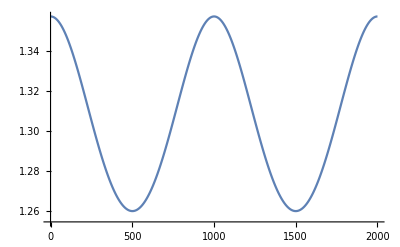

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will alwas retrieve the most up - to - date values.